```mathematica
X=Table[0.05(n-1),{n,21}]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

```mathematica
YD=List[0,0.00974,0.0758,0.213,0.369,0.503,0.608,0.687,0.746,0.791,0.825,0.852,0.874,0.891,0.905,0.917,0.926,0.934,0.941,0.947,0.952]
```

{0,0.00974,0.0758,0.213,0.369,0.503,0.608,0.687,0.746,0.791,0.825,0.852,0.874,0.891,0.905,0.917,0.926,0.934,0.941,0.947,0.952}

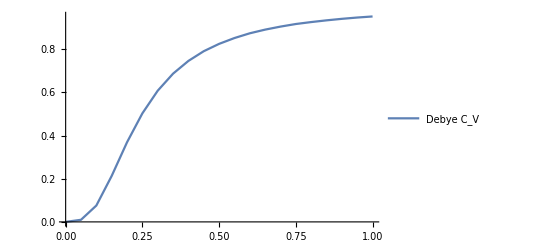

```mathematica
debye=ListPlot[Transpose[{X,YD}],Joined->True,PlotStyle->ColorData[97,1],PlotLegends->LineLegend[{ColorData[97,1]},{"Debye " Subscript[C, V]}]]
```

```mathematica
YE[x_]:=(x^2 Exp[x])/(Exp[x] - 1)^2
```

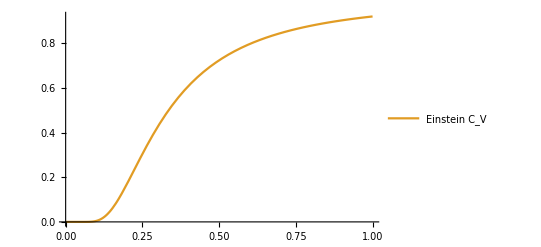

```mathematica
einstein=Plot[YE[1/x],{x,0,1},PlotStyle->ColorData[97,2],PlotLegends->LineLegend[{ColorData[97,2]},{"Einstein " Subscript[C, V]}]]
```

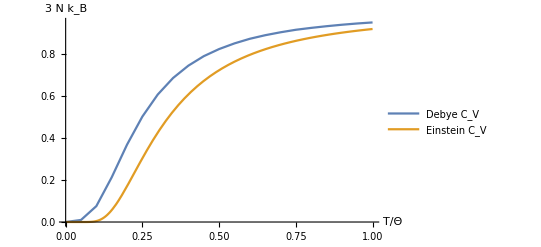

```mathematica
d6=Show[debye,einstein,AxesLabel->{T/Θ,3 N Subscript[k, B]}]
```

```mathematica
Kn=1/3; Kp=1/6
```

1/6

```mathematica
omegap[qa_] :=Sqrt[Kn+Kp+Sqrt[Kn^2+2Cos[2qa] Kn Kp + Kp^2]]
```

```mathematica
omegam[qa_] :=Sqrt[Kn+Kp-Sqrt[Kn^2+2Cos[2qa] Kn Kp + Kp^2]]
```

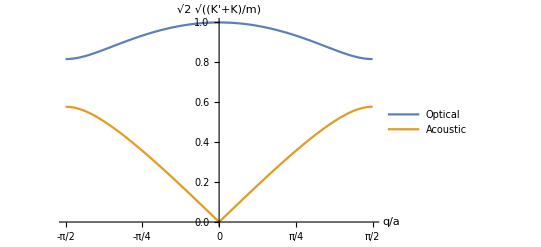

```mathematica
Plot[{omegap[qa],omegam[qa]},{qa,-Pi/2,Pi/2},Ticks->{Range[-Pi/2,Pi/2,Pi/4],Automatic},AxesLabel->{q/a,Sqrt[2(K + K')/m]},PlotLegends->{"Optical","Acoustic"}]
```